```mathematica
(*data ve formátu:{{počet bitů kolize,doba hledání},{.,.},...}*)
data={{0,2133},{0,3472},{0,1948},{0,1858},{0,1852},{0,1835},{0,1831},{0,1832},{0,1832},{0,1831},{0,1824},{0,1803},{0,1818},{0,1813},{0,1833},{0,1857},{0,1813},{0,1808},{0,1812},{0,1812},{0,1825},{0,1844},{0,1824},{0,1813},{0,1814},{0,1860},{0,1817},{0,1812},{0,1819},{0,1816},{1,2361},{1,3340},{1,1910},{1,1833},{1,1824},{1,2328},{1,2329},{1,1851},{1,3393},{1,4393},{1,2367},{1,3345},{1,2870},{1,2866},{1,1820},{1,2838},{1,1822},{1,2335},{1,1832},{1,1805},{1,2359},{1,2872},{1,1815},{1,1849},{1,2326},{1,2343},{1,2365},{1,5387},{1,2842},{1,2353},{2,5351},{2,1787},{2,1838},{2,2323},{2,2355},{2,4866},{2,1859},{2,1805},{2,2882},{2,4341},{2,2319},{2,2813},{2,2340},{2,4865},{2,2328},{2,2850},{2,4321},{2,5854},{2,4316},{2,4367},{2,2890},{2,4847},{2,2841},{2,3318},{2,1819},{2,2855},{2,3317},{2,3359},{2,1823},{2,2800},{3,1818},{3,2380},{3,6810},{3,1839},{3,3880},{3,5323},{3,4838},{3,5789},{3,7815},{3,10794},{3,7831},{3,10378},{3,14850},{3,5294},{3,6347},{3,10900},{3,3842},{3,5848},{3,2351},{3,3385},{3,5373},{3,10275},{3,6781},{3,3816},{3,5386},{3,10848},{3,4310},{3,26698},{3,2824},{3,6829},{4,7344},{4,4862},{4,2327},{4,10782},{4,12781},{4,1788},{4,12727},{4,4351},{4,14269},{4,15803},{4,5306},{4,16247},{4,23282},{4,14286},{4,9329},{4,2331},{4,1807},{4,14823},{4,7347},{4,13343},{4,20764},{4,6853},{4,6309},{4,20304},{4,10799},{4,2376},{4,8791},{4,1793},{4,14231},{4,12276},{5,40757},{5,18783},{5,5826},{5,3345},{5,14276},{5,3352},{5,22723},{5,10375},{5,15799},{5,30267},{5,64523},{5,95167},{5,26629},{5,28308},{5,9323},{5,5341},{5,36686},{5,21223},{5,2822},{5,21253},{5,10772},{5,28217},{5,19833},{5,44156},{5,9817},{5,9296},{5,5800},{5,22214},{5,12786},{5,12765},{6,67049},{6,25293},{6,25799},{6,15353},{6,9809},{6,22339},{6,48131},{6,44189},{6,15292},{6,99669},{6,16780},{6,105138},{6,16283},{6,64528},{6,3323},{6,6818},{6,26260},{6,36858},{6,34103},{6,52995},{6,77086},{6,41427},{6,7297},{6,4112},{6,130602},{6,73958},{6,12740},{6,8964},{6,21894},{6,12761},{7,22840},{7,107049},{7,57418},{7,14126},{7,8051},{7,219006},{7,24361},{7,3968},{7,66642},{7,140476},{7,47236},{7,27340},{7,55843},{7,22823},{7,27823},{7,18287},{7,73178},{7,14349},{7,59079},{7,14279},{7,94945},{7,42717},{7,12318},{7,28266},{7,151929},{7,5825},{7,18286},{7,34166},{7,70236},{7,31738},{8,5365},{8,48670},{8,18751},{8,168333},{8,50060},{8,46043},{8,25686},{8,103175},{8,46104},{8,119095},{8,10284},{8,85875},{8,62134},{8,9783},{8,223607},{8,178229},{8,107282},{8,128147},{8,16811},{8,44541},{8,9326},{8,46903},{8,9772},{8,14761},{8,406093},{8,317723},{8,72749},{8,249426},{8,123022},{8,179359},{9,475906},{9,43957},{9,182506},{9,383199},{9,77375},{9,521073},{9,295872},{9,322404},{9,126551},{9,322196},{9,55482},{9,126824},{9,100402},{9,252572},{9,529124},{9,11307},{9,874315},{9,14788},{9,417054},{9,437364},{9,505098},{9,168406},{9,389776},{9,73971},{9,199709},{9,17805},{9,147262},{9,414389},{9,90393},{9,296841},{10,228792},{10,468053},{10,39148},{10,544003},{10,1919500},{10,39516},{10,87377},{10,352164},{10,420053},{10,705204},{10,885190},{10,35577},{10,741905},{10,1351796},{10,203331},{10,218706},{10,452485},{10,386847},{10,870871},{10,161903},{10,787023},{10,654406},{10,1074285},{10,125696},{10,139749},{10,770399},{10,246683},{10,1848261},{10,144453},{10,36649},{11,564647},{11,2330046},{11,120117},{11,1965782},{11,669217},{11,1428459},{11,190876},{11,56001},{11,945910},{11,2636832},{11,1316059},{11,4421615},{11,1451538},{11,174149},{11,692001},{11,2996853},{11,705818},{11,537859},{11,3018961},{11,161477},{11,2037586},{11,2212787},{11,328624},{11,119769},{11,36491},{11,3863010},{11,256296},{11,378524},{11,297399},{11,1385039},{12,1075708},{12,612107},{12,2820455},{12,2168305},{12,428921},{12,487798},{12,1904107},{12,1382349},{12,2787168},{12,1239981},{12,4880091},{12,4549225},{12,5819808},{12,4399885},{12,56858},{12,1367581},{12,384018},{12,459551},{12,1986259},{12,2170379},{12,3355317},{12,1700336},{12,1375215},{12,133074},{12,1764912},{12,2101798},{12,1270030},{12,489312},{12,580056},{12,122178},{13,3449067},{13,2531285},{13,1168001},{13,2011799},{13,1731485},{13,10104421},{13,5611875},{13,5683316},{13,7427498},{13,706382},{13,24239038},{13,161019},{13,1581389},{13,3579760},{13,4081072},{13,2629315},{13,1336090},{13,140838},{13,926502},{13,5730744},{13,947257},{13,864572},{13,4427014},{13,3220207},{13,4015713},{13,4151184},{13,2313088},{13,4079393},{13,1712513},{13,54906},{14,31151643},{14,1480620},{14,5212318},{14,11346778},{14,2102833},{14,347646},{14,26367305},{14,5356418},{14,368233},{14,1283351},{14,10410356},{14,4655737},{14,4844434},{14,9219408},{14,1714720},{14,1302239},{14,1397758},{14,7693528},{14,11898467},{14,15709396},{14,6389945},{14,7890769},{14,5514491},{14,631390},{14,7766246},{14,5325841},{14,16462731},{14,19334024},{14,3659789},{14,9163587},{15,9711578},{15,12761394},{15,13443925},{15,2382420},{15,4568100},{15,48056704},{15,25166388},{15,10000016},{15,13979078},{15,30266658},{15,2215250},{15,20369489},{15,8063442},{15,9590563},{15,10384600},{15,50231567},{15,29614958},{15,46030287},{15,8789561},{15,7625539},{15,32196313},{15,8247069},{15,4878059},{15,15657994},{15,16840},{15,22104301},{15,17210877},{15,20493584},{15,5971408},{15,3969274},{16,4424483},{16,16706},{16,57521831},{16,14873393},{16,17895162},{16,13427340},{16,9741045},{16,7779497},{16,67905374},{16,26975525},{16,21837161},{16,69480992},{16,12305626},{16,14095690},{16,2669917},{16,28614418},{16,62321486},{16,6701290},{16,41773056},{16,52506955},{16,23314766},{16,10191955},{16,41397261},{16,63779359},{16,99027972},{16,18528158},{16,419547},{16,16213874},{16,44787077},{16,11415994},{17,149983740},{17,7651218},{17,27664403},{17,10391521},{17,83838768},{17,38757306},{17,84366378},{17,18564139},{17,41250040},{17,2077455},{17,114712220},{17,319683759},{17,13901721},{17,10502946},{17,38055062},{17,61114409},{17,19783344},{17,73478013},{17,42531268},{17,89158849},{17,7416652},{17,76853793},{17,3097372},{17,43920192},{17,31014499},{17,68975969},{17,158831921},{17,93883916},{17,32451774},{17,84666607},{18,376376904},{18,154662307},{18,166333255},{18,554561548},{18,108267282},{18,102322372},{18,3334280},{18,53813422},{18,53707061},{18,5128718},{18,165085694},{18,326117255},{18,162514614},{18,81425153},{18,9091329},{18,326337947},{18,17681695},{18,49879678},{18,43485263},{18,6310079},{18,25819572},{18,154044752},{18,158315555},{18,121284963},{18,57022782},{18,202450515},{18,75643830},{18,107240577},{18,56658346},{18,27739790},{19,538253466},{19,163408877},{19,174197010},{19,252901179},{19,6893811},{19,86951817},{19,349723340},{19,386253993},{19,10694581},{19,314282171},{19,321753421},{19,116139595},{19,683375440},{19,58549451},{19,758502059},{19,501973584},{19,56076311},{19,85359549},{19,119663927},{19,286961310},{19,1149839},{19,346587040},{19,17388899},{19,510156337},{19,996238211},{19,196397837},{19,14821648},{19,37771486},{19,65105661},{19,465628611},{20,981453344},{20,110230855},{20,1920012044},{20,28831580},{20,1271974398},{20,1005080602},{20,151396001},{20,191375359},{20,224586592},{20,610441083},{20,107165076},{20,976660335},{20,151384403},{20,193373766},{20,629011200},{20,1129284565},{20,1178634717},{20,500001198},{20,392660504},{20,426735697},{20,27719672},{20,1698984102},{20,695532582},{20,507016514},{20,157258778},{20,1292277881},{20,387783564},{20,1505697305},{20,418470834},{20,1372040417},{21,2819817744},{21,3988790313},{21,1694525406},{21,1072788111},{21,1857894806},{21,981394014},{21,397939452},{21,2013103283},{21,3126391923},{21,4067057566},{21,366751200},{21,191419253},{21,776292472},{21,2269264316},{21,909798580},{21,3682915612},{21,6778980533},{21,725945011},{21,1431113013},{21,611609776},{21,1564182376},{21,2656363307},{21,29048906},{21,1271574854},{21,1861435349},{21,892246334},{21,1837192422},{21,437181305},{21,505242800},{21,1869500565},{22,361382370},{22,2529551424},{22,193570182},{22,310223164},{22,9406924709},{22,361496010},{22,1345273583},{22,1218123804},{22,807568498},{22,4019683403},{22,5462309663},{22,6303157616},{22,1220375913},{22,857468746},{22,3856796514},{22,1302726140},{22,446129713},{22,33317236},{22,2787974094},{22,268483136},{22,2470489967},{22,973762158},{22,260438335},{22,8829274934},{22,3368886078},{22,4669799275},{22,1739743289},{22,6021813148},{22,3821293646},{22,4299322067},{23,3021686693},{23,1114737952},{23,3769042756},{23,2699922428},{23,5025431507},{23,10166093531},{23,927089177},{23,11425658353},{23,6587455698},{23,4569517613},{23,16043747928},{23,4804811992},{23,1183441871},{23,7118358069},{23,6375004765},{23,10020289726},{23,952725859},{23,10461277077},{23,5817028243},{23,3577004592},{23,5418311894},{23,9176914478},{23,12912210599},{23,22996434704},{23,3751310863},{23,3651954452},{23,7502246558},{23,6690514412},{23,15423273212},{23,4727371752}};
maxBits = 23;
```

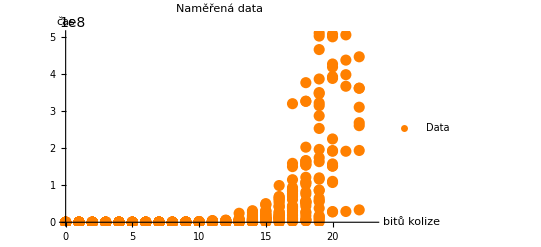

```mathematica
varListPlot=ListPlot[data,PlotLabel->"Naměřená data",AxesLabel->{"bitů kolize","čas"},PlotStyle->{Orange,PointSize[0.02]},PlotLegends->{"Data"}]
```

```mathematica
(*funkce,která nám bude modelovat dobu hledání*)
function:=a*2^(b*x)
(*nalezení parametrů a,b*)
foundVars=FindFit[data,function,{a,b},{x}]
(*dosazení parametrů do funkce*)
foundFunction:=function/. foundVars
```

{a→57.8479,b→1.16595}

Model doby hledání x bitů kolize: 57.8479 2^(1.16595 x)

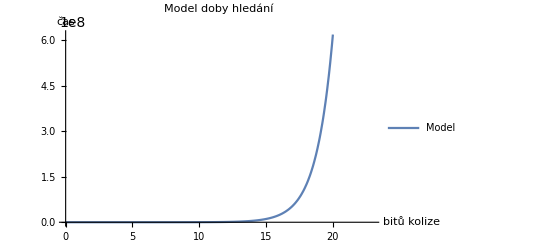

```mathematica
Print["Model doby hledání x bitů kolize: ",foundFunction]
(*vykreslíme model*)
plotFunction=Plot[foundFunction,{x,0,maxBits},PlotLabel->"Model doby hledání",AxesLabel->{"bitů kolize","čas"},PlotLegends->{"Model"}]
```

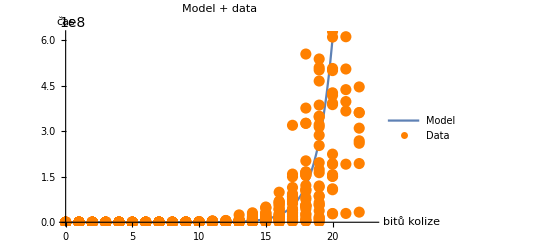

```mathematica
(*vykreslíme model a přes ně naměřená data (zda model sedí)*)
Show[plotFunction,varListPlot,PlotLabel->"Model + data"]
```

```mathematica
(*Doba hledání plné kolize:do funkce dosadíme x=512*)
time = foundFunction/. x->512;
timeQuantity = Quantity[time,"Nanoseconds"];
Print["512 bitů kolize se bude hledat: ",timeQuantity]
Print["512 bitů kolize se bude hledat: ", UnitConvert[timeQuantity,"Seconds"]]
Print["512 bitů kolize se bude hledat: ", UnitConvert[timeQuantity,"Years"]]
Print["512 bitů kolize se bude hledat: ", UnitConvert[timeQuantity,"Centuries"]]
Print["512 bitů kolize se bude hledat: ", UnitConvert[timeQuantity,"Millennia"]]
universeAge = 13.7*10^9 * 365*24*60*60*1000*1000*1000; (* in nanoseconds *)
Print["512 bitů kolize se bude hledat: ", time / universeAge , " universe's ages"]
```

512 bitů kolize se bude hledat: 2.93451×10^181 ns

512 bitů kolize se bude hledat: 2.93451×10^172 s

512 bitů kolize se bude hledat: 9.30527×10^164 yr

512 bitů kolize se bude hledat: 9.2991×10^162 centuries

512 bitů kolize se bude hledat: 9.2991×10^161 millennia

512 bitů kolize se bude hledat: 6.79217×10^154 universe's ages